```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={d>0,p>d,θ<π,θ>-π};
```

```mathematica
df[ζ_]=k((1-d^2/ζ^2)^(θ/π))/(√(p^2-ζ^2));
```

```mathematica
f0[ζ_]=∫df[ζ]ⅆζ+c//FullSimplify
```

c+(k π (1-d^2/ζ^2)^(θ/π) ζ (1-ζ^2/d^2)^(-θ/π) AppellF1[1/2-θ/π,1/2,-θ/π,3/2-θ/π,ζ^2/p^2,ζ^2/d^2])/(p (π-2 θ))

```mathematica
f0[ζ_]= c+(k π (ζ^2-d^2)^(θ/π) ζ^(1-2 θ/π) (1-ζ^2/d^2)^(-θ/π) AppellF1[1/2-θ/π,1/2,-θ/π,3/2-θ/π,ζ^2/p^2,ζ^2/d^2])/(p (π-2 θ))
```

c+(k π ζ^(1-(2 θ)/π) (-d^2+ζ^2)^(θ/π) (1-ζ^2/d^2)^(-θ/π) AppellF1[1/2-θ/π,1/2,-θ/π,3/2-θ/π,ζ^2/p^2,ζ^2/d^2])/(p (π-2 θ))

```mathematica
λ[ζ_]=1-Exp[-ζ];
f[ζ_]=f0[λ[ζ]];
```

```mathematica
f[0]//Simplify
```

c+(0^(1-(2 θ)/π) (-d^2)^(θ/π) k π)/(p (π-2 θ))

```mathematica
c=0;
```

```mathematica
Solve[{f[d]==-ⅈ w,f[p]==-ⅈ h},{d,p}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{((1-ⅇ^-d)^(1-(2 θ)/π) (-d^2+(1-ⅇ^-d)^2)^(θ/π) (1-((1-ⅇ^-d)^2)/d^2)^(-θ/π) k π AppellF1[1/2-θ/π,1/2,-θ/π,3/2-θ/π,((1-ⅇ^-d)^2)/p^2,((1-ⅇ^-d)^2)/d^2])/(p (π-2 θ))==-ⅈ w,((1-ⅇ^-p)^(1-(2 θ)/π) (-d^2+(1-ⅇ^-p)^2)^(θ/π) (1-((1-ⅇ^-p)^2)/d^2)^(-θ/π) k π AppellF1[1/2-θ/π,1/2,-θ/π,3/2-θ/π,((1-ⅇ^-p)^2)/p^2,((1-ⅇ^-p)^2)/d^2])/(p (π-2 θ))==-ⅈ h},{d,p}]

```mathematica
f[ζ_]=f0[λ[ζ]];
```

```mathematica
Block[{k=1,c=0,d=1,p=2,θ=20*π/180},ParametricPlot[ReIm@f[ξ+ⅈ η],{ξ,0,3},{η,0,π}]]
```

$Aborted

```mathematica
(* Condition for d: Re@f[L]=L when L->∞ *)
Limit[(Re@f[L])/L,L->∞](*==1*)
```

Re[K]

```mathematica
(*d= K  d/1 ;->K=1*)
```

```mathematica
K=1;
```

```mathematica
(* 
dz: height hinge to y=0
du: height y=0 to horizontal mirror
du+dz = flap height.
*)
```

```mathematica
c=-(dz+du) Tan[θ]+ⅈ du;
d= √π((dz-ⅈ c) ⅇ^(-ⅈ θ))/(Gamma[1+θ/π] Gamma[1/2-θ/π]);
```

(ⅇ^(-ⅈ θ) √π (dz-ⅈ (ⅈ du+(-du-dz) Tan[θ])))/(Gamma[1/2-θ/π] Gamma[1+θ/π])

```mathematica
(* Check that the hinge position is correct: *)
Block[{dz=.6,du = .0,θ =20*π/180},{f[.00001],f[-ⅈ d+.000001]}]
```

{-0.218238+1.38916×10^-21 ⅈ,2.21622×10^-7-0.6 ⅈ}

```mathematica
(* Check that the map does not move far away from the wavemaker: *)
```

```mathematica
Block[{dz=.6,du = .0},{f[20]/.θ ->20*π/180,f[20]/.θ ->-20*π/180}]
```

{19.9985+2.79901×10^-15 ⅈ,20.0029-2.97357×10^-15 ⅈ}

```mathematica
(* Check that f and df are consistent: *)
Block[{dz=.6,du = .0,θ =20*π/180},  {df[.4-.34ⅈ],f'[.4-.34ⅈ]}]
```

{1.04439+0.0816258 ⅈ,1.04439+0.0816258 ⅈ}

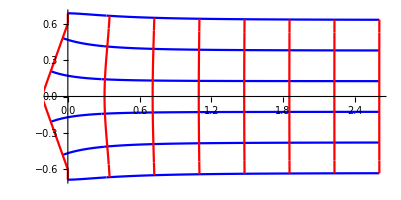

```mathematica
Block[{dz=.6,du = .0,θ =20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

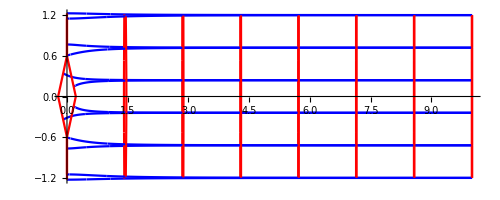

```mathematica
Show[Block[{dz=.6,du = .0,θ =20*π/180,lim={.00001,10,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]],
Block[{dz=.6,du = .0,θ =-20*π/180,lim={.00001,10,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]]
```

```mathematica
(* Time derivative: *)
θ=Θ[t];
```

```mathematica
d=.;
```

```mathematica
dft=D[df[ζ], t]
```

((1+d^2/ζ^2)^(Θ[t]/π) Log[1+d^2/ζ^2] Θ'[t])/π

```mathematica
∫dftⅆζ//FullSimplify
```

(d (d^2+d^4/ζ^2)^(Θ[t]/π) (-1/ζ^2)^(3/2) ζ (d^2+ζ^2)^(1-Θ[t]/π) (1+ζ^2/d^2)^(Θ[t]/π) (π HypergeometricPFQ[{3/2,1+Θ[t]/π,1+Θ[t]/π},{2+Θ[t]/π,2+Θ[t]/π},1+d^2/ζ^2]-Hypergeometric2F1[3/2,(π+Θ[t])/π,2+Θ[t]/π,1+d^2/ζ^2] Log[1+d^2/ζ^2] (π+Θ[t])) Θ'[t])/(2 (π+Θ[t])^2)

```mathematica
-∫D[df[ζ], t]/df[ζ] ⅆζ//FullSimplify
```

-((2 d ArcTan[ζ/d]+ζ Log[1+d^2/ζ^2]) Θ'[t])/π